```mathematica
SetDirectory@NotebookDirectory[]
Import["esmlib_nsl.wl"]
```

/home/eric/git/nonlinear-systems-lab

```mathematica
ClearAll[eqn1]
eqn1=θ''[t]+2 Τ θ'[t]+Sin[θ[t]]==0;
eqn1//TraditionalForm
```

θ''(t)+2 Τ θ'(t)+sin(θ(t))==0

## Equilibria

```mathematica
sol=Solve[{eqn1,θ'[t]==θ''[t]==0}];
sol//TraditionalForm
```

{{θ'(t)→0,θ''(t)→0,θ(t)→ConditionalExpression[2 π c_1,c_1∈ℤ]},{θ'(t)→0,θ''(t)→0,θ(t)→ConditionalExpression[2 π c_1+π,c_1∈ℤ]}}

## Linearize

```mathematica
thpp[t_]:=θ''[t]/.Solve[eqn1,θ''[t]][[1]]
thpp[t]//TraditionalForm
```

-2 Τ θ'(t)-sin(θ(t))

```mathematica
Series[thpp[t],{θ'[t],0,1},{θ[t],0,1}]
```

(-θ[t]+O[θ[t]]^2)-2 Τ θ'[t]+O[θ'[t]]^2

```mathematica
Eigenvalues[({{0, 1}, {-1, -2Τ}})]
Eigenvalues[({{0, 1}, {1, -2Τ}})]
```

{-Τ-√(-1+Τ^2),-Τ+√(-1+Τ^2)}

{-Τ-√(1+Τ^2),-Τ+√(1+Τ^2)}

## Misc

### Breaking Things

```mathematica
eqn=x''[t]==-x[t]+x'[t]^3
```

x''[t]==-x[t]+x'[t]^3

{x[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

{x[t]}

{InterpolatingFunction[{{0., 100.}}, <>][t][t]}

{t,0.,100.}

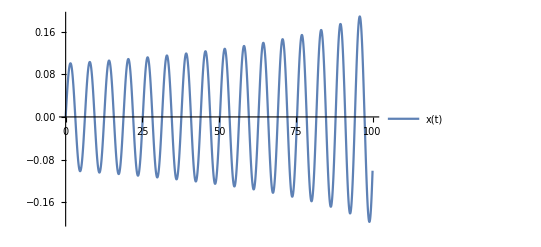

```mathematica
sol=NDSolve[{eqn,x[0]==0,x'[0]==.1},{x[t]},{t,0,100}][[1]]
IFPlot[sol]
```

{x[t]}

{InterpolatingFunction[{{0., 32.3027}}, <>][t][t]}

{t,0.,32.3027}

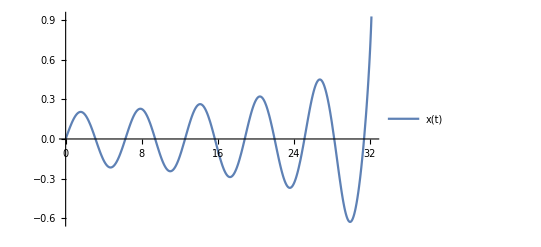

```mathematica
IFPlot[sol]
```

```mathematica
(x[t]/.sol)[[0,1]]
```

{{0.,32.3027}}

### How NSolve works

```mathematica
NSolve[x+y==5,x]
```

{{x→5.-1. y}}

### Graphics

```mathematica
Manipulate[StreamPlot[{w,-2t w-Sin[th]},{th,-5,5},{w,-5,5}],{{t,0},-1,1}]
```